```mathematica
Determination of the Gibbs Dividing Surface
```

```mathematica
Double SAM 0%
```

```mathematica
PathMD="/home/eixeres/Downloads/Densmaps_Double/densmaps_double/densmaps_s0/";
s0sam = Import[PathMD<>"s0_sam_nozeros.dat"];
Length[s0sam]
```

494

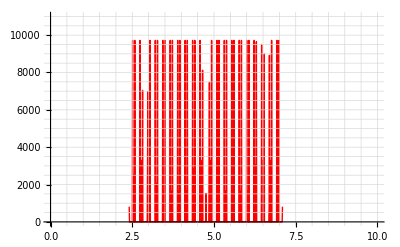

```mathematica
plots0sam=ListPlot[s0sam,Joined->True,PlotRange->{{0,10},{0,11000}}, PlotStyle->{Red,Thick},GridLines->{{0,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8,8.5, 9, 9.5,10},{500, 1000, 1500, 2000, 2500, 3000, 3500, 4000, 4500, 5000, 5500, 6000, 6500, 7000, 7500, 8000,8500, 9000, 9500, 10000, 10500, 11000}}]
```

```mathematica
means0sam = Mean[s0sam]
```

{4.75031,925.63}

```mathematica
sums0sam=Integrate[Interpolation[s0sam][x],{x,2.40606,7.09456}]/925.6304991902833
```

4.68677

```mathematica
PathMD="/home/eixeres/Downloads/Densmaps_Double/densmaps_double/densmaps_s0/";
s0water = Import[PathMD<>"s0_water.dat"];
Length[s0water]
```

1000

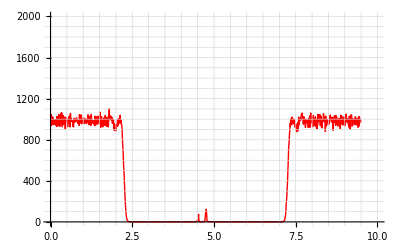

```mathematica
plots0water=ListPlot[s0water,Joined->True,PlotRange->{{0,10},{0,2000}}, PlotStyle->{Red,Thick},GridLines->{{0,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8,8.5, 9, 9.5,10},{100, 200, 300, 400, 500, 600, 700, 800, 900, 1000, 1100, 1200, 1300, 1400, 1500, 1600, 1700, 1800, 1900, 2000}}]
```

```mathematica
sums0water=Integrate[Interpolation[s0water][x],{x,0,9.50063}]/1000
```

4.41081

```mathematica
sum1s0=Integrate[1,{x,0,9.50063}]
```

9.50063

```mathematica
totals0=sum1s0-sums0water-sums0sam
```

0.403051

```mathematica
ds0=totals0/2
```

0.201525

```mathematica
Double SAM 5%
```

```mathematica
PathMD="/home/eixeres/Downloads/Densmaps_Double/densmaps_double/densmaps_s5/";
s5sam = Import[PathMD<>"s5_sam_nozeros.dat"];
Length[s5sam]
```

514

```mathematica
plots0sam=ListPlot[s0sam,Joined->True,PlotRange->{{0,10},{0,11000}}, PlotStyle->{Red,Thick},GridLines->{{0,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8,8.5, 9, 9.5,10},{500, 1000, 1500, 2000, 2500, 3000, 3500, 4000, 4500, 5000, 5500, 6000, 6500, 7000, 7500, 8000,8500, 9000, 9500, 10000, 10500, 11000}}]
```

-Graphics-

```mathematica
means5sam = Mean[s5sam]
```

{4.8627,1027.26}

```mathematica
sums5sam=Integrate[Interpolation[s5sam][x],{x,2.36564,7.35975}]/1027.2590414396886
```

4.98774

```mathematica
PathMD="/home/eixeres/Downloads/Densmaps_Double/densmaps_double/densmaps_s5/";
s5water = Import[PathMD<>"s5_water.dat"];
Length[s5water]
```

1000

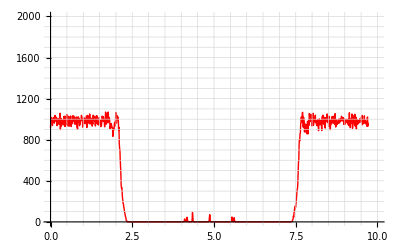

```mathematica
plots5water=ListPlot[s5water,Joined->True,PlotRange->{{0,10},{0,2000}}, PlotStyle->{Red,Thick},GridLines->{{0,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8,8.5, 9, 9.5,10},{100, 200, 300, 400, 500, 600, 700, 800, 900, 1000, 1100, 1200, 1300, 1400, 1500, 1600, 1700, 1800, 1900, 2000}}]
```

```mathematica
sums5water=Integrate[Interpolation[s5water][x],{x,0,9.72539}]/1000
```

4.24377

```mathematica
totals5=9.72539-sums5water-sums5sam
```

0.493878

```mathematica
ds5=totals5/2
```

0.246939

```mathematica
Double SAM 11%
```

```mathematica
PathMD="/home/eixeres/Downloads/Densmaps_Double/densmaps_double/densmaps_s11/";
s11sam = Import[PathMD<>"s11_sam_nozeros.dat"];
Length[s11sam]
```

518

```mathematica
PathMD="/home/eixeres/Downloads/Densmaps_Double/densmaps_double/densmaps_s11/";
s11water = Import[PathMD<>"s11_water.dat"];
Length[s11water]
```

1000

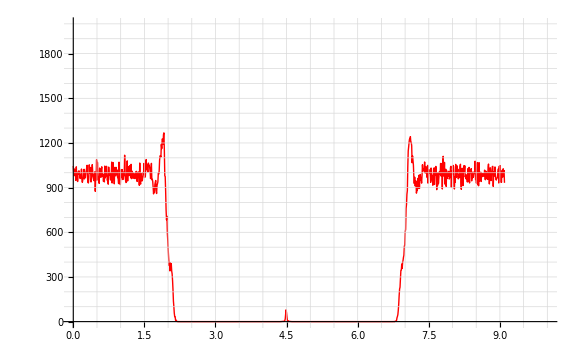

```mathematica
plots11water=ListPlot[s11water,Joined->True,PlotRange->{{0,10},{0,2000}}, PlotStyle->{Red,Thick},GridLines->{{0,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8,8.5, 9, 9.5,10},{100, 200, 300, 400, 500, 600, 700, 800, 900, 1000, 1100, 1200, 1300, 1400, 1500, 1600, 1700, 1800, 1900, 2000}}]
```

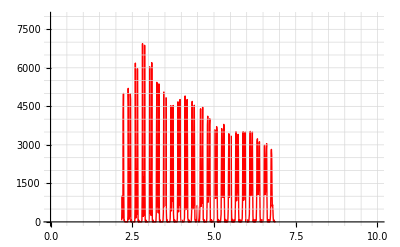

```mathematica
plots11sam=ListPlot[s11sam,Joined->True,PlotRange->{{0,10},{0,8000}}, PlotStyle->{Red,Thick},GridLines->{{0,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8,8.5, 9, 9.5,10},{500, 1000, 1500, 2000, 2500, 3000, 3500, 4000, 4500, 5000, 5500, 6000, 6500, 7000, 7500, 8000}}]
```

```mathematica
means11sam = Mean[s11sam]
```

{4.5299,964.56}

```mathematica
sums11sam=Integrate[Interpolation[s11sam][x],{x,2.17618,6.88363}]/964.5600326235522
```

4.71656

```mathematica
sums11water=Integrate[Interpolation[s11water][x],{x,0,9.09623}]/1000
```

4.14345

```mathematica
totals11=9.09623-sums11water-sums11sam
```

0.23622

```mathematica
ds11=totals11/2
```

0.11811

```mathematica
Double SAM 17%
```

```mathematica
PathMD="/home/eixeres/Downloads/Densmaps_Double/densmaps_double/densmaps_s17/";
s17sam = Import[PathMD<>"s17_sam_nozeros.dat"];
Length[s17sam]
```

517

```mathematica
PathMD="/home/eixeres/Downloads/Densmaps_Double/densmaps_double/densmaps_s17/";
s17water = Import[PathMD<>"s17_water.dat"];
Length[s17water]
```

1000

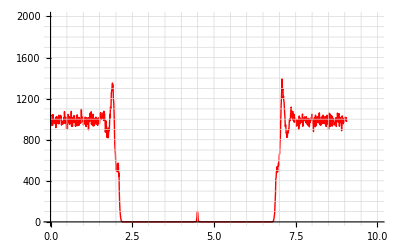

```mathematica
plots17water=ListPlot[s17water,Joined->True,PlotRange->{{0,10},{0,2000}}, PlotStyle->{Red,Thick},GridLines->{{0,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8,8.5, 9, 9.5,10},{100, 200, 300, 400, 500, 600, 700, 800, 900, 1000, 1100, 1200, 1300, 1400, 1500, 1600, 1700, 1800, 1900, 2000}}]
```

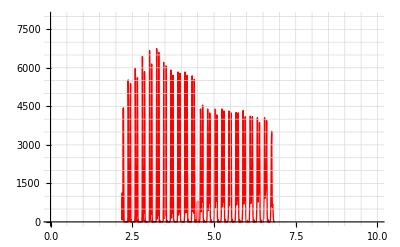

```mathematica
plots17sam=ListPlot[s17sam,Joined->True,PlotRange->{{0,10},{0,8000}}, PlotStyle->{Red,Thick},GridLines->{{0,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8,8.5, 9, 9.5,10},{500, 1000, 1500, 2000, 2500, 3000, 3500, 4000, 4500, 5000, 5500, 6000, 6500, 7000, 7500, 8000}}]
```

```mathematica
means17sam = Mean[s17sam]
```

{4.51518,971.206}

```mathematica
sums17sam=Integrate[Interpolation[s17sam][x],{x,2.17599,6.85437}]/971.205705589942
```

4.68722

```mathematica
sums17water=Integrate[Interpolation[s17water][x],{x,0,9.05756}]/1000
```

4.15181

```mathematica
totals17=9.05756-sums17water-sums17sam
```

0.218527

```mathematica
ds17=totals17/2
```

0.109263

```mathematica
Double SAM 33%
```

```mathematica
PathMD="/home/eixeres/Downloads/Densmaps_Double/densmaps_double/densmaps_s33/";
s33sam = Import[PathMD<>"s33_sam_nozeros.dat"];
Length[s33sam]
```

520

```mathematica
PathMD="/home/eixeres/Downloads/Densmaps_Double/densmaps_double/densmaps_s33/";
s33water = Import[PathMD<>"s33_water.dat"];
Length[s33water]
```

1000

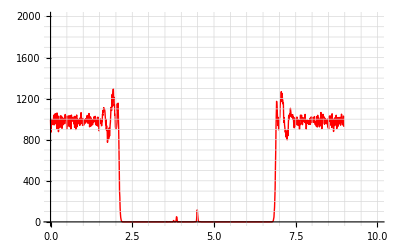

```mathematica
plots33water=ListPlot[s33water,Joined->True,PlotRange->{{0,10},{0,2000}}, PlotStyle->{Red,Thick},GridLines->{{0,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8,8.5, 9, 9.5,10},{100, 200, 300, 400, 500, 600, 700, 800, 900, 1000, 1100, 1200, 1300, 1400, 1500, 1600, 1700, 1800, 1900, 2000}}]
```

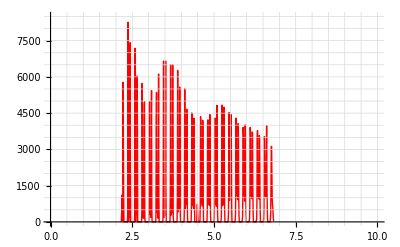

```mathematica
plots33sam=ListPlot[s33sam,Joined->True,PlotRange->{{0,10},{0,8500}}, PlotStyle->{Red,Thick},GridLines->{{0,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8,8.5, 9, 9.5,10},{500, 1000, 1500, 2000, 2500, 3000, 3500, 4000, 4500, 5000, 5500, 6000, 6500, 7000, 7500, 8000,8500}}]
```

```mathematica
means33sam = Mean[s33sam]
```

{4.49472,975.322}

```mathematica
sums33sam=Integrate[Interpolation[s33sam][x],{x,2.16429,6.82514}]/975.3224234615385
```

4.67022

```mathematica
sums33water=Integrate[Interpolation[s33water][x],{x,0,8.97147}]/1000
```

4.17808

```mathematica
totals33=8.97147-sums33water-sums33sam
```

0.12317

```mathematica
ds33=totals33/2
```

0.0615852

```mathematica
Double SAM 66%
```

```mathematica
PathMD="/home/eixeres/Downloads/Densmaps_Double/densmaps_double/densmaps_s66/";
s66sam = Import[PathMD<>"s66_sam_nozeros.dat"];
Length[s66sam]
```

523

```mathematica
PathMD="/home/eixeres/Downloads/Densmaps_Double/densmaps_double/densmaps_s66/";
s66water = Import[PathMD<>"s66_water.dat"];
Length[s66water]
```

1000

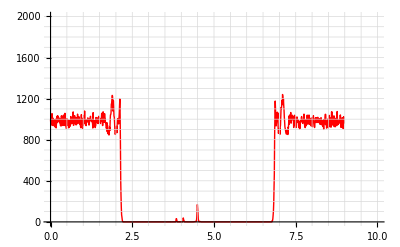

```mathematica
plots66water=ListPlot[s66water,Joined->True,PlotRange->{{0,10},{0,2000}}, PlotStyle->{Red,Thick},GridLines->{{0,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8,8.5, 9, 9.5,10},{100, 200, 300, 400, 500, 600, 700, 800, 900, 1000, 1100, 1200, 1300, 1400, 1500, 1600, 1700, 1800, 1900, 2000}}]
```

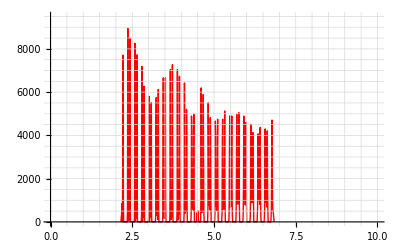

```mathematica
plots66sam=ListPlot[s66sam,Joined->True,PlotRange->{{0,10},{0,9500}}, PlotStyle->{Red,Thick},GridLines->{{0,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8,8.5, 9, 9.5,10},{500, 1000, 1500, 2000, 2500, 3000, 3500, 4000, 4500, 5000, 5500, 6000, 6500, 7000, 7500, 8000,8500, 9000, 9500}}]
```

```mathematica
means66sam = Mean[s66sam]
```

{4.50061,972.53}

```mathematica
sums66sam=Integrate[Interpolation[s66sam][x],{x,2.15598,6.84524}]/972.5304336902485
```

4.69848

```mathematica
sums66water=Integrate[Interpolation[s66water][x],{x,0,8.97427}]/1000
```

4.22057

```mathematica
totals66=8.97427-sums66water-sums66sam
```

0.0552165

```mathematica
ds66=totals66/2
```

0.0276083

```mathematica
SAM 11% water 1000
```

```mathematica
PathMD="/home/eixeres/Downloads/Densmaps_Double/densmaps_double/g_density_s11_w1000/";
s11w1water = Import[PathMD<>"s11_w1000_water.dat"];
Length[s11w1water]
```

1000

```mathematica
PathMD="/home/eixeres/Downloads/Densmaps_Double/densmaps_double/g_density_s11_w1000/";
s11w1sam = Import[PathMD<>"s11_w1000_sam.dat"];
Length[s11w1sam]
```

1000

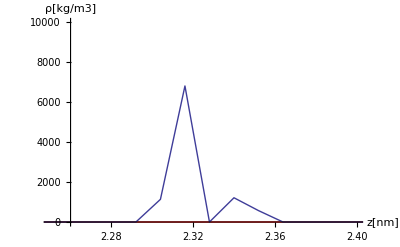

```mathematica
plots11w1water=ListPlot[s11w1water,Joined->True,PlotRange->{{2.25,2.4},{0,10000}}, PlotStyle->Red];
plots11w1sam=ListPlot[s11w1sam,Joined->True,PlotRange->{{2.2,2.4},{0,10000}}];
Show[plots11w1water,plots11w1sam,AxesLabel->{"z[nm]","ρ[kg/m3]"}]
```

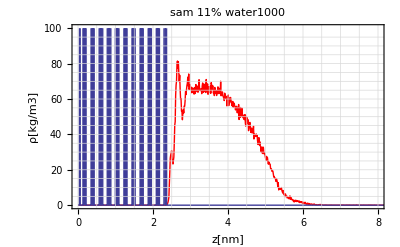

```mathematica
pls11w1water=ListPlot[s11w1water,Joined->True,PlotRange->{{0,8},{0,100}}, PlotStyle->{Red,Thick},GridLines->{{0,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8},{5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95}}];
pls11w1sam=ListPlot[s11w1sam,Joined->True,PlotRange->{{0,8},{0,100}},PlotStyle->Thick];
Show[pls11w1water,pls11w1sam,PlotLabel->"sam 11% water1000",AxesLabel->{"z[nm]","ρ[kg/m3]"},Frame->True]
```

```mathematica
TESTS
```

```mathematica
Comparing the surface SAM 11% of the "w1000" case with the "double" case (and using for the first one 2500 slices with g_density
```

```mathematica
s11w1000 finer
```

```mathematica
PathMD="/home/eixeres/Downloads/Densmaps_Double/densmaps_double/";
s11w1sam2 = Import[PathMD<>"s11_sam_finer.dat"];
Length[s11w1sam2]
```

Import::nffil: File not found during Import.

0

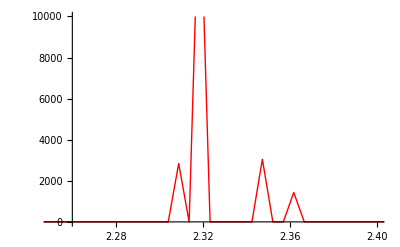

```mathematica
ps11w1water=ListPlot[s11w1sam2,Joined->True,PlotRange->{{2.25,2.4},{0,10000}}, PlotStyle->Red]
```

```mathematica
s11_double (OLD)
```

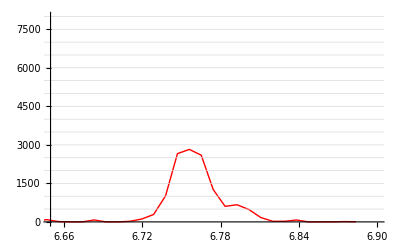

```mathematica
plots11sam=ListPlot[s11sam,Joined->True,PlotRange->{{6.65,6.9},{0,8000}}, PlotStyle->{Red},GridLines->{{0,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8,8.5, 9, 9.5,10},{500, 1000, 1500, 2000, 2500, 3000, 3500, 4000, 4500, 5000, 5500, 6000, 6500, 7000, 7500, 8000}}]
```

```mathematica
g_density of double SAM  0%: comparisson of our result with one got from using g-density with 2500 slices and taking only 5ns  (before mistake: 20ns!!)
```

```mathematica
NEW
```

```mathematica
PathMD="/home/eixeres/Downloads/Densmaps_Double/densmaps_double/";
deletethis = Import[PathMD<>"dens2_NPT_double.dat"];
Length[deletethis]
```

1000

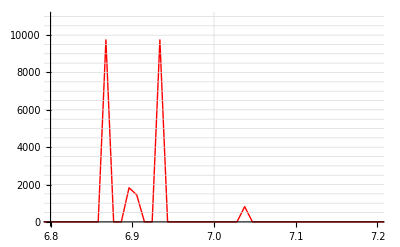

```mathematica
ListPlot[deletethis,Joined->True,PlotRange->{{6.8,7.2},{0,11000}}, PlotStyle->{Red,Thick},GridLines->{{0,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8,8.5, 9, 9.5,10},{500, 1000, 1500, 2000, 2500, 3000, 3500, 4000, 4500, 5000, 5500, 6000, 6500, 7000, 7500, 8000,8500, 9000, 9500, 10000, 10500, 11000}}]
```

```mathematica
OLD
```

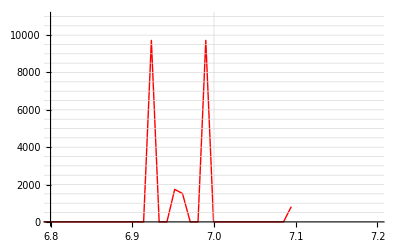

```mathematica
plots0sam=ListPlot[s0sam,Joined->True,PlotRange->{{6.8,7.2},{0,11000}}, PlotStyle->{Red,Thick},GridLines->{{0,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8,8.5, 9, 9.5,10},{500, 1000, 1500, 2000, 2500, 3000, 3500, 4000, 4500, 5000, 5500, 6000, 6500, 7000, 7500, 8000,8500, 9000, 9500, 10000, 10500, 11000}}]
```